```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of April 3, 2014, 16:23:56.0784.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
NumberOfCrossings[b_BR]:=Length[SignsOfCrossings[b]]
SignsOfCrossings[b_BR]:=(* return a list of +1 and -1s, indicating the signs of the crossings *)
Sign/@(b⟦2⟧)
```

```mathematica
CubeOfResolutions[BR[Knot["4 1"]]]//TableForm
```

Resolution[BR[3,{-1,2,-1,2}],{0,0,0,0},{{17,2,10},{19,8,16},{12,14,18,4,6}}]
Resolution[BR[3,{-1,2,-1,2}],{0,0,0,1},{{17,2,10},{19,8,13,15,18,12,4,6}}]
Resolution[BR[3,{-1,2,-1,2}],{0,0,1,0},{{19,8,16},{18,4,6,11,14,17,2,9}}]
Resolution[BR[3,{-1,2,-1,2}],{0,0,1,1},{{11,17,19,8,13,15,18,2,9,4,6}}]
Resolution[BR[3,{-1,2,-1,2}],{0,1,0,0},{{17,2,10},{4,5,14,18,7,12,16,19}}]
Resolution[BR[3,{-1,2,-1,2}],{0,1,0,1},{{13,7,12},{17,2,10},{15,18,19,4,5}}]
Resolution[BR[3,{-1,2,-1,2}],{0,1,1,0},{{11,14,17,2,9,18,4,5,19,7,16}}]
Resolution[BR[3,{-1,2,-1,2}],{0,1,1,1},{{15,18,19,4,5},{11,17,2,9,7,13}}]
Resolution[BR[3,{-1,2,-1,2}],{1,0,0,0},{{19,8,16},{18,12,14,3,6,10,1,17}}]
Resolution[BR[3,{-1,2,-1,2}],{1,0,0,1},{{15,18,10,1,17,12,3,6,19,8,13}}]
Resolution[BR[3,{-1,2,-1,2}],{1,0,1,0},{{9,3,6},{19,8,16},{11,14,18,1,17}}]
Resolution[BR[3,{-1,2,-1,2}],{1,0,1,1},{{9,3,6},{19,8,13,15,18,11,1,17}}]
Resolution[BR[3,{-1,2,-1,2}],{1,1,0,0},{{7,12,14,18,10,1,17,3,5,16,19}}]
Resolution[BR[3,{-1,2,-1,2}],{1,1,0,1},{{13,7,12},{19,3,5,15,18,10,1,17}}]
Resolution[BR[3,{-1,2,-1,2}],{1,1,1,0},{{11,14,18,1,17},{16,19,3,5,7,9}}]
Resolution[BR[3,{-1,2,-1,2}],{1,1,1,1},{{7,9,19,3,5,15,18,1,17,11,13}}]

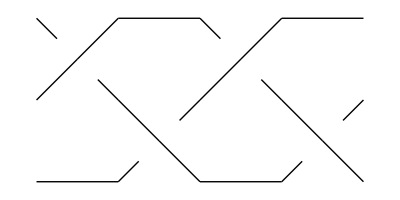

```mathematica
BraidPlot[BR[Knot[4,1]]]
```

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
productToList[X_Times]:=List@@X
productToList[X_]:={X}
```

```mathematica
productToList[(f[1,2,3]g[4,5,6])]
```

{f[1,2,3],g[4,5,6]}

```mathematica
productToList[(f[1,2,3])]
```

{f[1,2,3]}

```mathematica
Product[
R[{4*i+2-0,4*i+4-0},z[i,3],z[i+1,3]]
,{i,0,4-1}]
```

R[{2,4},z[0,3],z[1,3]] R[{6,8},z[1,3],z[2,3]] R[{10,12},z[2,3],z[3,3]] R[{14,16},z[3,3],z[4,3]]

```mathematica
BR[Knot["3 1"]]
```

BR[2,{-1,-1,-1}]

```mathematica
ResolutionCircles[BR[Knot["3 1"]],{0,0,1}]
```

R$16712[{2},S$16712[z$16712[0,0],z$16712[1,0]]]
R$16712[{4},S$16712[z$16712[0,1],z$16712[1,1]]]
R$16712[{6},S$16712[z$16712[1,0],z$16712[2,0]]]
R$16712[{8},S$16712[z$16712[1,1],z$16712[2,1]]]
R$16712[{9},S$16712[z$16712[2,0],z$16712[2,1]]]
R$16712[{11},S$16712[z$16712[3,0],z$16712[3,1]]]
R$16712[{13},S$16712[z$16712[0,0],z$16712[3,0]]]
R$16712[{14},S$16712[z$16712[0,1],z$16712[3,1]]]

{{14,4,8,11,13,9,2,6}}

```mathematica
ResolutionCircles[BR[Knot["3 1"]],{1,1,1}]
```

R$15810[{1},S$15810[z$15810[0,0],z$15810[0,1]]]
R$15810[{3},S$15810[z$15810[1,0],z$15810[1,1]]]
R$15810[{5},S$15810[z$15810[1,0],z$15810[1,1]]]
R$15810[{7},S$15810[z$15810[2,0],z$15810[2,1]]]
R$15810[{9},S$15810[z$15810[2,0],z$15810[2,1]]]
R$15810[{11},S$15810[z$15810[3,0],z$15810[3,1]]]
R$15810[{13},S$15810[z$15810[0,0],z$15810[3,0]]]
R$15810[{14},S$15810[z$15810[0,1],z$15810[3,1]]]

{{3,5},{7,9},{1,13,11,14}}

```mathematica
Product
```

```mathematica
Product[S[z[5,k],z[1,k]],{k,0,4}]
```

S[z[5,0],z[1,0]] S[z[5,1],z[1,1]] S[z[5,2],z[1,2]] S[z[5,3],z[1,3]] S[z[5,4],z[1,4]]

```mathematica
BraidProduct[generator_Integer,type_Integer]:=Module[
{},

];
```

```mathematica
Map
```

```mathematica
Tuples[{0,1},5]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
BasisVectors[r_Resolution]:=
```

```mathematica
HomologicalGrading[b_BasisVector]:=
```

```mathematica
HomologicalGrading[b_BasisVector]:=
```

```mathematica
EulerGrading[b_BasisVector]:=
```

```mathematica
BasisVector[resolution, signs]
```

```mathematica
Times[{1,2,2}]
```

{1,2,2}

```mathematica
Differential[b_BasisVector]:=
```

```mathematica
AllBasisVectorsInCGrading[s_Integer,r_Integer]:=
```

```mathematica
DifferentialsAsMatrix[b_BR,s+Intefer,r_Integer]:=
```

```mathematica
KhRepresentativesInGrading[b_BR,s_Integer,r_Integer]:=
```

```mathematica
KhInGrading[b_BR,s_Integer,r_Integer]:=
```

```mathematica
Kh[b]:=
```